```mathematica
ClearAll["Global`*"];
orthog[m_,n_]:=
Module[{σ,a,b,Ja,w,xi},
σ=Table[0.,{i,1,2n},{j,1,2n}];
Do[σ[[2,i+1]]=m[[i+1]],{i,0,2n-1}];

a=Table[0.,{i,1,n}];b=a;
a[[1]]=m[[2]]/m[[1]];
b[[1]]=0;

Do[
Do[
σ[[i+2,j+1]]=σ[[i+1,j+2]]-a[[i]]σ[[i+1,j+1]]-b[[i]]σ[[i,j+1]];
a[[i+1]]=-σ[[i+1,i+1]]/σ[[i+1,i]]+σ[[i+2,i+2]]/σ[[i+2,i+1]];
b[[i+1]]=σ[[i+2,i+1]]/σ[[i+1,i]];
(*If[σ[[i+2,i+1]]==0,Print["warning 0!"]];
If[σ[[i+2,i+2]]==0,Print["2 warning 0!"]];*)
,{j,i,2n-i-1}];
,{i,1,n-1}];

Ja=Table[0,{i,1,n},{j,1,n}];

Do[
Ja[[i,i]]=a[[i]];
,{i,1,n}];

Do[
Ja[[i,i+1]]=-(Abs[b[[i+1]]])^(1/2);
Ja[[i+1,i]]=-(Abs[b[[i+1]]])^(1/2);
,{i,1,n-1}];

w=Table[0,{i,1,n}];
xi=Table[0,{i,1,n}];
eval=Eigenvalues[Ja];
evec=Eigenvectors[Ja];

Do[
w[[i]]=evec[[i,1]]^2 m[[1]];
,{i,1,n}];
{eval,w}
];
```

```mathematica
(* Say R and Rdot are initially normally distributed *)
μR=1;
σR=2;
μRd=0.1;
σRd=1.1;
rho=0.1;

c=0;

RRdPDF=BinormalDistribution[{μR,μRd},{σR,σRd},rho];
momRRd[i_,j_]:=Moment[RRdPDF,{i,j}];

rhs[mom_]:={
0,
c mom[0,0]-mom[0,1]-mom[1,0],
2(c mom[0,1]-mom[0,2]-mom[1,1]),
3(c mom[0,2]-mom[0,3]-mom[1,2]),
mom[0,1],
mom[0,2]+1(c mom[1,0]-mom[1,1]-mom[2,0]),
(mom[0,3]+2(c mom[1,1]-mom[1,2]-mom[2,1])),
(mom[0,4]+3(c mom[1,2]-mom[1,3]-mom[2,2])),
2 mom[1,1],
(3 mom[2,1])
};
rhs0[mom_]:={
0,
c mom[0,0]-mom[0,1]-mom[1,0],
2(c mom[0,1]-mom[0,2]-mom[1,1]),
0,
mom[0,1],
mom[0,2]+1(c mom[1,0]-mom[1,1]-mom[2,0]),
0,
0,
2 mom[1,1],
0
};
```

```mathematica
n=2;
ks=Flatten[{Table[{q,p},{q,0,n-1},{p,0,2n-1}],
Table[{q,p},{q,n,2n-1},{p,0,0}]}
,2];
ic=Table[momRRd[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
moms=ic;
moms2=moms;
dt=1 10^-3;
Nt=5000;

sol={};solexact={};
Do[
AppendTo[sol,moms];
AppendTo[solexact,moms2];

mymomRRd[q_,p_]:=moms[[First[First[Position[ks,{q,p}]]]]];
mymomRRdex[q_,p_]:=moms2[[First[First[Position[ks,{q,p}]]]]];
mRs=Table[mymomRRd[i,0],{i,0,2n-1}];
{xi,w}=orthog[mRs,n];
v=Table[
Table[xi[[i]]^j,{i,1,n}]
,{j,0,n-1}];
r1=DiagonalMatrix[w];
Do[ms[m]=Table[mymomRRd[i,m],{i,0,n-1}],{m,0,2n-1}];
Do[condmoms[i]=LinearSolve[v.r1,ms[i]],{i,0,2n-1}]
Do[condmomvec[j]=Table[condmoms[i][[j]],{i,0,2n-1}];,{j,1,n}];
Do[
{xis[i],ws[i]}=orthog[condmomvec[i],n];
,{i,1,n}];
Do[wtot[i,j]=w[[j]]ws[j][[i]],{i,1,n},{j,1,n}];
mom[q_,p_]:=Sum[wtot[i,j] xi[[j]]^q(xis[j][[i]])^p,{i,1,n},{j,1,n}];
y1=moms+dt/2 rhs[mom];
yex=moms2+dt/2 rhs0[mymomRRdex];
mymomRRdex[q_,p_]:=yex[[First[First[Position[ks,{q,p}]]]]];
mymomRRd[q_,p_]:=y1[[First[First[Position[ks,{q,p}]]]]];

(* stage 2 *)
mRs=Table[mymomRRd[i,0],{i,0,2n-1}];
{xi,w}=orthog[mRs,n];
v=Table[
Table[xi[[i]]^j,{i,1,n}]
,{j,0,n-1}];
r1=DiagonalMatrix[w];
Do[ms[m]=Table[mymomRRd[i,m],{i,0,n-1}],{m,0,2n-1}];
Do[condmoms[i]=LinearSolve[v.r1,ms[i]],{i,0,2n-1}]
Do[condmomvec[j]=Table[condmoms[i][[j]],{i,0,2n-1}];,{j,1,n}];
Do[
{xis[i],ws[i]}=orthog[condmomvec[i],n];
,{i,1,n}];
Do[wtot[i,j]=w[[j]]ws[j][[i]],{i,1,n},{j,1,n}];
mom[q_,p_]:=Sum[wtot[i,j] xi[[j]]^q(xis[j][[i]])^p,{i,1,n},{j,1,n}];

moms=moms+dt rhs[mom];
moms2=moms2+dt rhs0[mymomRRdex];

(*moms=moms+dt rhs;*)
(*moms2=moms2+dt rhs0[mymomRRdex];*)
,{ts,1,Nt}];
```

```mathematica
rhs[mom]
```

{0,-1.1,-3.08,-4.884,0.1,-4.1,-4.044,-20.4756,0.64,2.82}

```mathematica
moms2
yex
```

{1,0.1,1.22,0.364,1,0.32,1.264,1.1692,5,13}

{1,0.09945,1.21846,0.361558,1.00005,0.31795,{},{},5.00032,{}}

```mathematica
rhs[momRRd]
rhs[mom]
```

{0,-1.1,-3.08,-4.884,0.1,-4.1,-4.044,-17.897,0.64,2.82}

{0,-0.0058511,-0.005198,-0.00180826,0.0892805,0.0351935,0.00909279,0.00310885,-0.0740838,0.025926}

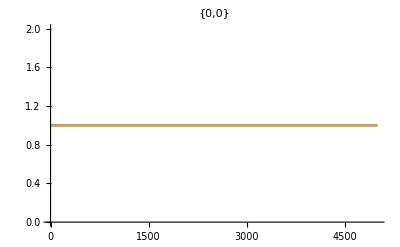
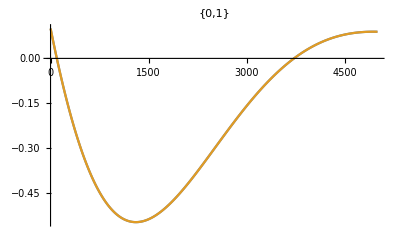
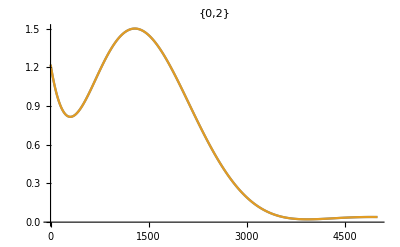
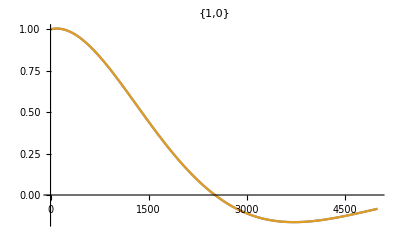
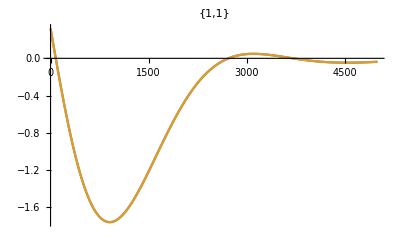
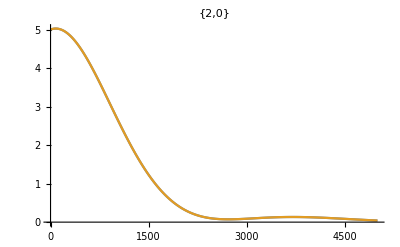

0

1.11022×10^-16

2.22045×10^-16

1.38778×10^-16

2.22045×10^-16

4.44089×10^-16

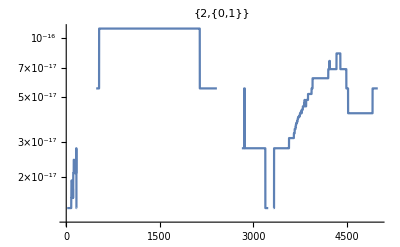
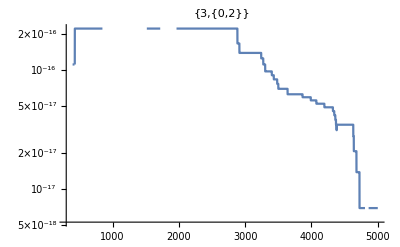
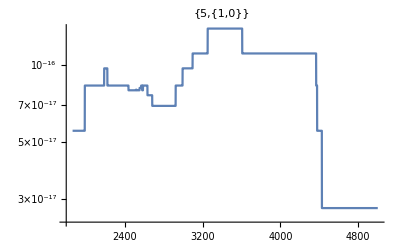
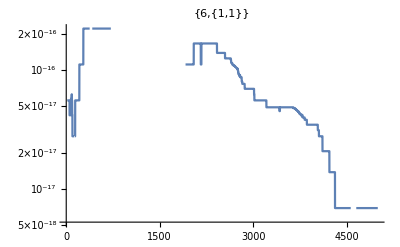
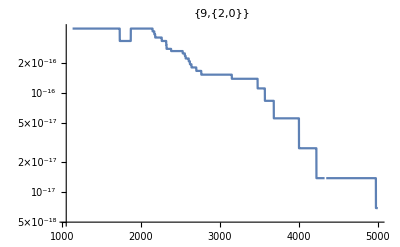
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<3,
AppendTo[plots,ListPlot[{sol[[All,i]],solexact[[All,i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
],
{i,1,Length[moms]}]
plots

plots={};
Do[
If[Total[ks[[i]]]<3,
AppendTo[plots,ListLogPlot[Abs[sol[[All,i]]-solexact[[All,i]]],Joined->True,PlotRange->All,PlotLabel->{i,ks[[i]]}]];
Print[ScientificForm[Max[Abs[sol[[All,i]]-solexact[[All,i]]]]]];
],
{i,1,Length[moms]}]
plots
```

```mathematica
ks//TableForm
```

0 | 0
0 | 1
0 | 2
0 | 3
1 | 0
1 | 1
1 | 2
1 | 3
2 | 0
3 | 0